```mathematica
(*---CaH6 氢笼 (12d Wyckoff) 紧束缚模型---*)
```

```mathematica
(*1. 基础参数设置*)
a0=3.3697998668513285;(*晶格常数*)
t1=-2.0;(*最近邻跳跃积分 eV*)
e0=0.0;(*在位能*)
```

```mathematica
(*2. 12d 原子坐标 (分数坐标)*)
hFracPos={
{0.25,0.00,0.50},{0.25,0.50,0.00},{0.50,0.25,0.00},
{0.00,0.25,0.50},{0.50,0.00,0.75},{0.00,0.50,0.75},
{0.75,0.50,0.00},{0.75,0.00,0.50},{0.00,0.75,0.50},
{0.50,0.75,0.00},{0.00,0.50,0.25},{0.50,0.00,0.25}
};
nAtoms=Length[hFracPos];
hCartPos=hFracPos*a0
```

{{0.84245,0.,1.6849},{0.84245,1.6849,0.},{1.6849,0.84245,0.},{0.,0.84245,1.6849},{1.6849,0.,2.52735},{0.,1.6849,2.52735},{2.52735,1.6849,0.},{2.52735,0.,1.6849},{0.,2.52735,1.6849},{1.6849,2.52735,0.},{0.,1.6849,0.84245},{1.6849,0.,0.84245}}

```mathematica
(*3. 寻找最近邻 (包含跨胞跳跃)*)
(*距离阈值设定为 a*sqrt(2)/4 附近*)
cutoff=1.2;
neighbors={};
Do[
Do[
distVec=(hCartPos[[j]]+{dx,dy,dz}*a0)-hCartPos[[i]];
dist=Norm[distVec];
If[0.1<dist<cutoff,
 (*`dist>0.1：排除掉“自己跳向自己”的情况*)
(*`dist<cutoff`这是紧束缚模型的关键，假设电子只能跳到很近的原子上，氢笼的最近邻距离大约是 $1.24$ Å，所以我们设置 cutoff=1.3。只有距离小于 1.3 的原子对才会被认为有“跳跃（Hopping）”发生。*)
AppendTo[neighbors,{i,j,{dx,dy,dz}}]
],
{i,nAtoms},{j,nAtoms}],
{dx,-1,1},{dy,-1,1},{dz,-1,1}
];
(*Do[Print["dx: ",dx,"  dy: ",dy,"  dz: ",dz],{dx,-1,1},{dy,-1,1},{dz,-1,1}] 可以用来理解Do的三重循环*)
```

```mathematica
adjMatrix=ConstantArray[0,{nAtoms,nAtoms}];
(*遍历找到的邻居列表，将对应位置设为 1*)
Do[
iIdx=neighbors[[idx,1]];
jIdx=neighbors[[idx,2]];
adjMatrix[[iIdx,jIdx]]=1,
{idx,Length[neighbors]}
];
(*4. 邻接矩阵展示*)
Print["--- 基于周期性边界条件的邻接矩阵 ---"];
Print["(1 表示在 1.3 Å 范围内存在跳跃路径)"];
adjMatrix//MatrixForm
Total[adjMatrix,{2}]//Print
(*5. 验证配位数*)
Print["每个原子的实际配位数 (邻接矩阵每行求和):"];
Total[adjMatrix,{2}]//Print
(*6. 打印具体的连接关系*)
Print["详细连接关系 (i -> j):"];
Table[
"H"<>ToString[i]<>" 可以跳向 -> "<>StringRiffle[Table["H"<>ToString[j],{j,Flatten[Position[adjMatrix[[i]],1]]}],", "],{i,nAtoms} ]//Column
```

--- 基于周期性边界条件的邻接矩阵 ---

(1 表示在 1.3 Å 范围内存在跳跃路径)

(0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0
0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0)

{4,4,4,4,4,4,4,4,4,4,4,4}

每个原子的实际配位数 (邻接矩阵每行求和):

{4,4,4,4,4,4,4,4,4,4,4,4}

详细连接关系 (i -> j):

H1 可以跳向 -> H4, H5, H9, H12
H2 可以跳向 -> H3, H6, H10, H11
H3 可以跳向 -> H2, H5, H7, H12
H4 可以跳向 -> H1, H6, H8, H11
H5 可以跳向 -> H1, H3, H8, H10
H6 可以跳向 -> H2, H4, H7, H9
H7 可以跳向 -> H3, H6, H10, H11
H8 可以跳向 -> H4, H5, H9, H12
H9 可以跳向 -> H1, H6, H8, H11
H10 可以跳向 -> H2, H5, H7, H12
H11 可以跳向 -> H2, H4, H7, H9
H12 可以跳向 -> H1, H3, H8, H10

```mathematica
(*4. 构造哈密顿矩阵 H(kx,ky,kz)*)
(*k 采用分数坐标单位 (即 2Pi/a 后的倍数)*)
Ham[kx_,ky_,kz_]:=Module[{H,kVec,phase},
H=IdentityMatrix[nAtoms]*e0;
kVec={kx,ky,kz};
Do[
i=neighbors[[idx,1]];
j=neighbors[[idx,2]];
R=neighbors[[idx,3]];
(*代码进入一个循环，遍历之前找出的所有邻居（neighbors）*)
(*对于每一条路径，它提取出：电子从哪个原子（i）跳到哪个原子（j），以及这个跳跃是否跨越了单元胞（R）*)
phase=Exp[I*2*Pi*(kVec.R)];
H[[i,j]]+=t1*phase,
{idx,Length[neighbors]}
];
H
];
(*查看 Gamma 点的解析矩阵*)
Print["Gamma 点哈密顿矩阵:"];
Ham[0,0,0]//MatrixForm
(*检查简并度*)
energyDataGamma=Sort[Eigenvalues[Ham[0,0,0]]]
(*对角项：电子待在原地。*)
(*非对角项：电子在不同原子间跳动，相位 $e^{i\mathbf{k}\cdot\mathbf{R}}$ 描述了晶格的相干性。*)
```

Gamma 点哈密顿矩阵:

(0. | 0. | 0. | -2. | -2. | 0. | 0. | 0. | -2. | 0. | 0. | -2.
0. | 0. | -2. | 0. | 0. | -2. | 0. | 0. | 0. | -2. | -2. | 0.
0. | -2. | 0. | 0. | -2. | 0. | -2. | 0. | 0. | 0. | 0. | -2.
-2. | 0. | 0. | 0. | 0. | -2. | 0. | -2. | 0. | 0. | -2. | 0.
-2. | 0. | -2. | 0. | 0. | 0. | 0. | -2. | 0. | -2. | 0. | 0.
0. | -2. | 0. | -2. | 0. | 0. | -2. | 0. | -2. | 0. | 0. | 0.
0. | 0. | -2. | 0. | 0. | -2. | 0. | 0. | 0. | -2. | -2. | 0.
0. | 0. | 0. | -2. | -2. | 0. | 0. | 0. | -2. | 0. | 0. | -2.
-2. | 0. | 0. | 0. | 0. | -2. | 0. | -2. | 0. | 0. | -2. | 0.
0. | -2. | 0. | 0. | -2. | 0. | -2. | 0. | 0. | 0. | 0. | -2.
0. | -2. | 0. | -2. | 0. | 0. | -2. | 0. | -2. | 0. | 0. | 0.
-2. | 0. | -2. | 0. | 0. | 0. | 0. | -2. | 0. | -2. | 0. | 0.)

{-8.,-4.,-4.,-1.1987×10^-15,-2.43022×10^-16,-1.5054×10^-17,2.57714×10^-16,4.77666×10^-16,1.15137×10^-15,4.,4.,8.}

```mathematica
(*5. 能带路径设置 (G-X-M-G-R)*)
pathPoints={
{0,0,0},(*G*)
{0,0.5,0},(*X*)
{0.5,0.5,0},(*M*)
{0,0,0},(*G*)
{0.5,0.5,0.5},(*R*)
{0,0.5,0} (*X*)
};
labels={"Γ","X","M","Γ","R", "X"};
segments=40;(*每段采点数*)
(*在高对称点之间进行线性插值，生成一条连续的 $k$ 空间采样路径。*)
kPath=Flatten[Table[
Table[pathPoints[[i]]+(pathPoints[[i+1]]-pathPoints[[i]])*t,
{t,0,1-1/segments,1/segments}], (*1-1/segments 是为了防止重复。因为第一段的终点就是第二段的起点，如果不减去最后一点，路径中就会出现两个坐标完全一样的 $X$ 点。*)
{i,Length[pathPoints]-1}],1];
AppendTo[kPath,Last[pathPoints]];
```

```mathematica
(*6. 计算能谱*)
energyData=Table[Sort[Eigenvalues[Ham@@k]],{k,kPath}];
(*1. Ham@@k (Apply 操作)
   *k 是路径中的一个坐标点，例如 {0.1,0,0}。
*Ham 函数定义时接收三个参数：Ham[kx_,ky_,kz_]。
*`@@` 是 Mathematica 的 “Apply” 符号。Ham@@{0.1,0,0} 等同于调用 Ham[0.1,0,0]。
*物理意义：根据当前位置 $k$，构造出那一处的 $12\times 12$ 哈密顿矩阵。
2. Eigenvalues[...] (求解特征值)
   *这是线性代数的核心：求解矩阵的特征值。
*物理意义：在量子力学中，哈密顿矩阵的特征值就是能量（Energy）。
*因为我们的矩阵是 $12\times 12$ 的，所以对于每一个 $k$ 点，它会返回 12 个能量值。
3. Sort[...] (排序)
   *Eigenvalues 返回的顺序通常是无序的（取决于数值算法）。
*物理意义：为了画出连续的能带，我们需要把这 12
个能量值从低到高排列。这样，最小的值连成第一条带，次小的连成第二条带，以此类推。如果不排序，画出来的能带图会像乱麻一样互相交叉跳跃。4. Table[...,{k,kPath}] (批处理循环)
   *这是一个循环，遍历我们之前在 kPath 中生成的所有采样点。
*物理意义：沿着我们设计的 $\Gamma\to X\to M\to\Gamma\to R$ 路线，一步一步地计算每一处的能级。*)
```

```mathematica
(*7. 绘图*)
(*自动计算费米能级：取第6带最高点和第7带最低点的平均值*)
```

```mathematica
Max[energyData[[All,6]]]
Min[energyData[[All,7]]]
```

1.25916×10^-15

-9.11268×10^-16

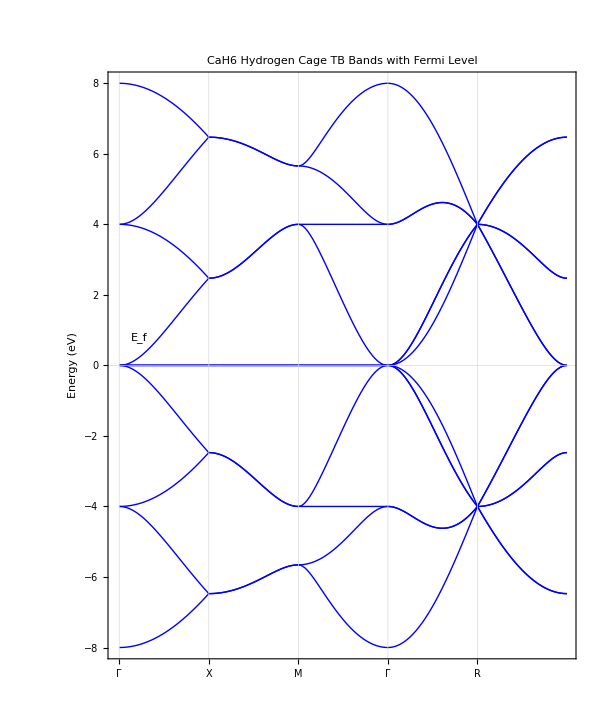

```mathematica
Ef=(Max[energyData[[All,6]]]+Min[energyData[[All,7]]])/2;
ListLinePlot[
Transpose[energyData],PlotRange->All,Frame->True,(*在垂直方向增加 Ef 的虚线*)
AspectRatio->1.2,
GridLines->{Table[i*segments+1,{i,0,4}],{Ef}},(*设置虚线的样式：y轴那条线设为红色虚线*)
Method->{"GridLinesInFront"->True},
LabelStyle->{FontSize->16,Bold,Black},
GridLinesStyle->{Directive[Gray,Dashed],Directive[Red,Thick,Dashed]},
FrameTicks->{{Automatic,None},{Table[{i*segments+1,Style[labels[[i+1]],16,Bold]},{i,0,4}],None}},
PlotStyle->Directive[Thick,Blue],FrameLabel->{None,"Energy (eV)"},
PlotLabel->"CaH6 Hydrogen Cage TB Bands with Fermi Level",ImageSize->600,(*使用 Epilog 在费米能级线上方写上 "Ef"*)Epilog->{Style[Text["\!\(\*SubscriptBox[\(E\), \(f\)]\)",{10,Ef+0.8}],Red,14,Bold]}
]
```